# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
Get["/Users/pcs/Desktop/Quantum channel/QMB_offline copy.wl"];
Get["/Users/pcs/Desktop/Quantum channel/Chaometer.wl"];
```

Get::noopen: Cannot open /Users/pcs/Desktop/Quantum channel/QMB_offline copy.wl.

```mathematica
KroneckerVectorProduct[a_,b_]:=Flatten[KroneckerProduct[a,b]];
BlochVector[ρ_]:=Tr[Pauli[#].ρ]&/@Range[3];
Parity[ψ_,L_]:=ψ[[FromDigits[Reverse[#],2]+1&/@Tuples[{0,1},L]]];
Braket[a_,b_]:=Conjugate[a].b;
MeanLevelSpacingRatio[eigenvalues_]:=Mean[Min/@Transpose[{#,1/#}]&[Ratios[Differences[eigenvalues]]]];
Clear[SurvivalProbability];
SurvivalProbability[ψt_,ψ0_]:=Abs[Braket[ψ0,ψt]]^2;
```

```mathematica
Clear[bloch];
bloch[rho_]:={2Re[rho[[1,2]]],-2Im[rho[[1,2]]],rho[[1,1]]-rho[[2,2]]};
(*Plot Bloch sphere with Bloch vector*)
plotsphere=SphericalPlot3D[1,{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Opacity[0.07],PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False];
plotsphere2=Graphics3D[{Opacity[0.3],Sphere[{0,0,0},1]}];
Clear[rho];
rho[vec_]:={{vec[[1]],vec[[2]]},{vec[[3]],vec[[4]]}};
Clear[haar];
haar[dim_Integer]:=Module[{l=2^dim,state1},
state1=Table[RandomReal[NormalDistribution[],2],{l}];
Normalize[state1[[All,1]]+I state1[[All,2]]]
];
(*Define the Pauli matrices*)
sx={{0,1},{1,0}};
sy={{0,-I},{I,0}};
sz={{1,0},{0,-1}};
(*Define collective spin operators for n spins*)
Clear[Jx,Jy,Jz];
Jx[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sx,IdentityMatrix[2]],{j,n}],{i,n}];
Jy[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sy,IdentityMatrix[2]],{j,n}],{i,n}];
Jz[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sz,IdentityMatrix[2]],{j,n}],{i,n}];
(*Define the Lipkin Hamiltonian*)
Clear[Hlmg];
Hlmg[α_,gx_,gy_,n_]:=α*Jz[n]+(gx/(n-1))(Jx[n].Jx[n])+(gy/(n-1))(Jy[n].Jy[n]);

Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(La),dimb=2^(Lb),rho},
rho=MatrixPartialTrace[state,2,{dima,dimb}];
Chop[Total[Map[VNentropy,Chop[Eigenvalues[rho]]]]]
];
Clear[svn];
svn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
(*Define subsystem dimensions*)
(*Compute the Page value using the digamma function*)
pageEntropy[La_,Lb_]:=PolyGamma[0,(2^La)(2^Lb)+1]-PolyGamma[0,(2^Lb)+1]-((2^La)-1)/(2*(2^Lb));
```

```mathematica
LaunchKernels[10]
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

# Hamiltonian scatter plots

```mathematica
L=10;
hx=1;
J=1;
hz=0.5;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
h1=h2=1;
Δ=1;
H=OpenXXZHamiltonian[L,Δ,h1,h2];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
Δ=1;
H=ClosedXXZHamiltonian[L,Δ];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
La=4;
Lb=L-La;
sdiageigenvec=ParallelTable[sdiag[L,La,Lb,i],{i,eigenvec},DistributedContexts->Full];
```

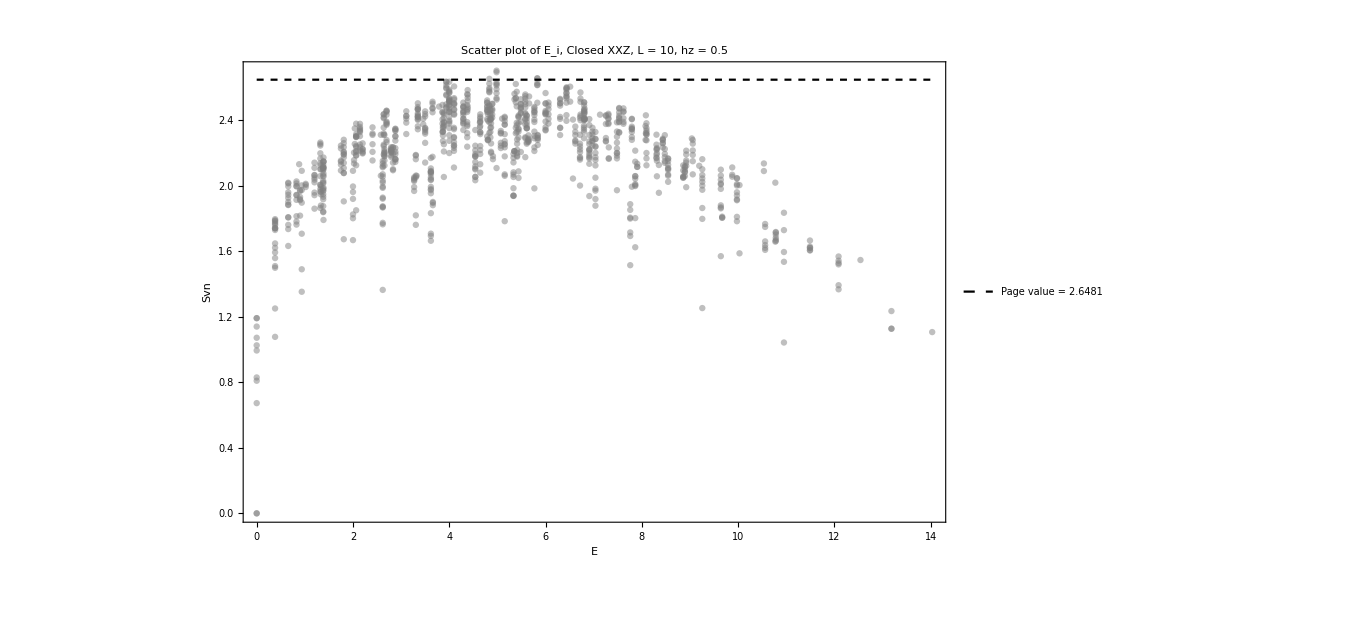

```mathematica
Show[{ListPlot[Transpose[{eigenval,sdiageigenvec}],PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of E_i, Closed XXZ, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",35,Black],PlotStyle->{Directive[Gray,Opacity[0.5]]},PlotRange->All,ImageSize->1000,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],Style["Svn"]}],Plot[pageEntropy[La,Lb],{x,Min[eigenval],Max[eigenval]},PlotStyle->{Directive[Black,Dashed]},PlotLegends->{Style["Page value = "<>ToString[N[pageEntropy[La,Lb]]],20,Black]}]},PlotRange->All]
```

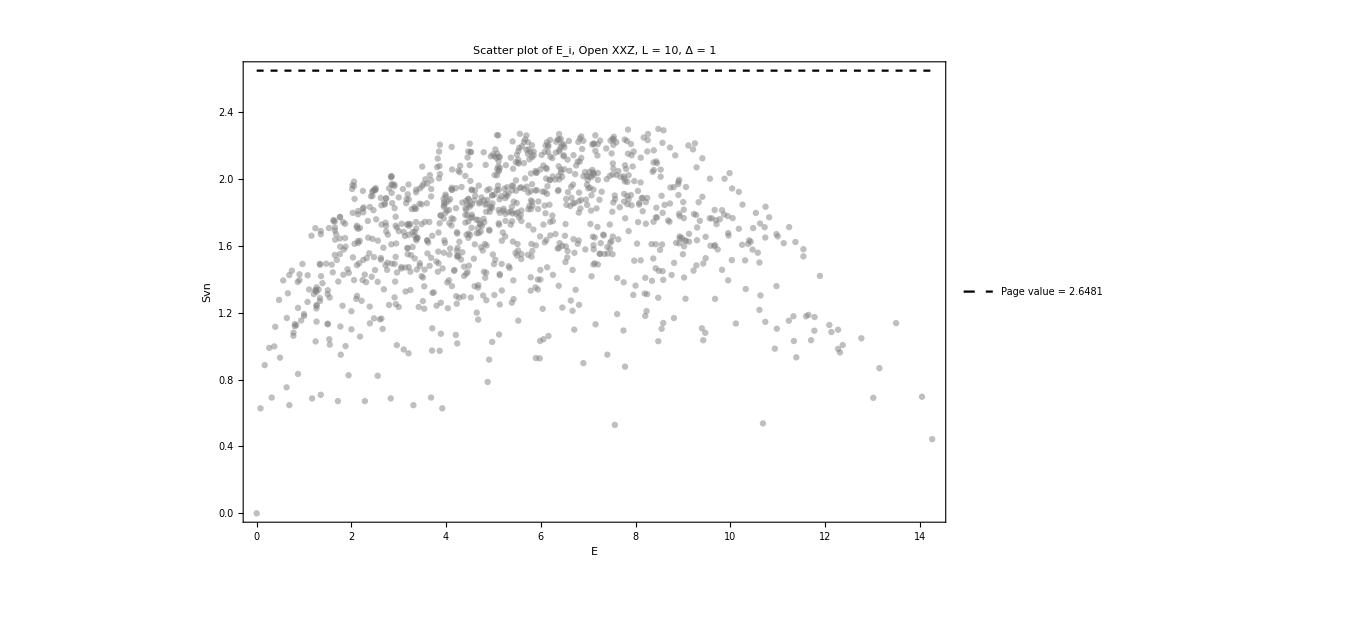

```mathematica
Show[{ListPlot[Transpose[{eigenval,sdiageigenvec}],PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of E_i, Open XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",35,Black],PlotStyle->{Directive[Gray,Opacity[0.5]]},PlotRange->All,ImageSize->1000,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],Style["Svn"]}],Plot[pageEntropy[La,Lb],{x,Min[eigenval],Max[eigenval]},PlotStyle->{Directive[Black,Dashed]},PlotLegends->{Style["Page value = "<>ToString[N[pageEntropy[La,Lb]]],20,Black]}]},PlotRange->All]
```

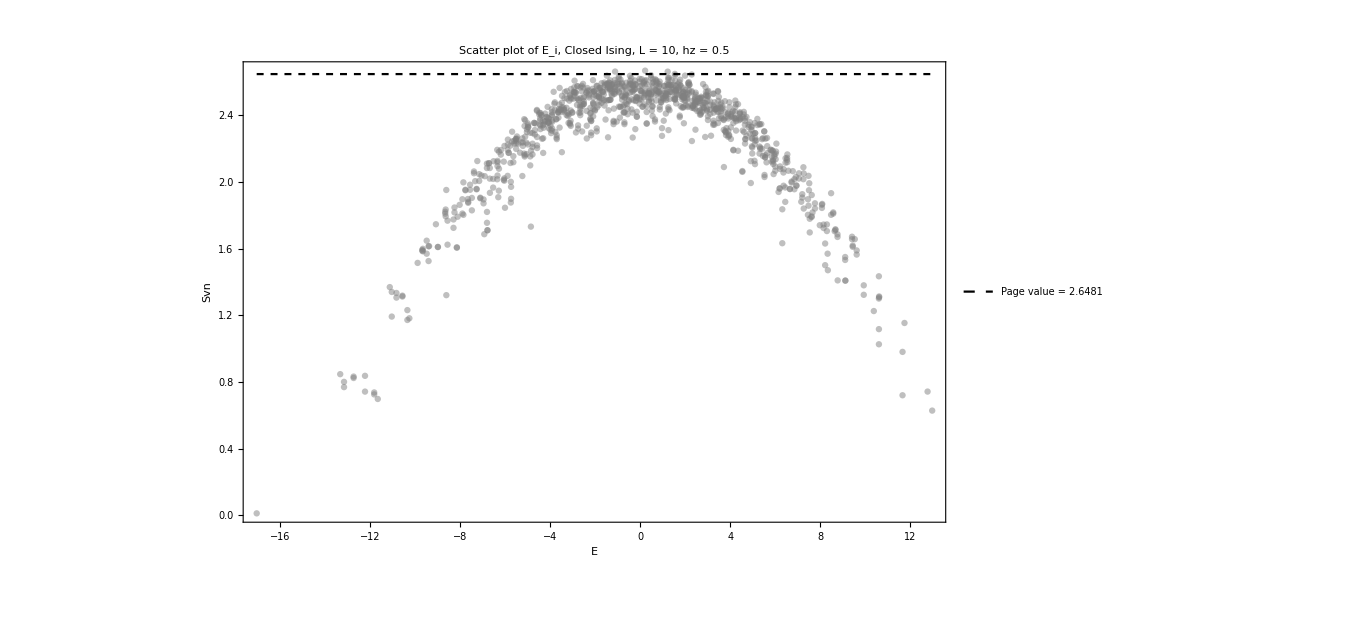

```mathematica
Show[{ListPlot[Transpose[{eigenval,sdiageigenvec}],PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of E_i, Closed Ising, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",35,Black],PlotStyle->{Directive[Gray,Opacity[0.5]]},PlotRange->All,ImageSize->1000,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],Style["Svn"]}],Plot[pageEntropy[La,Lb],{x,Min[eigenval],Max[eigenval]},PlotStyle->{Directive[Black,Dashed]},PlotLegends->{Style["Page value = "<>ToString[N[pageEntropy[La,Lb]]],20,Black]}]},PlotRange->All]
```

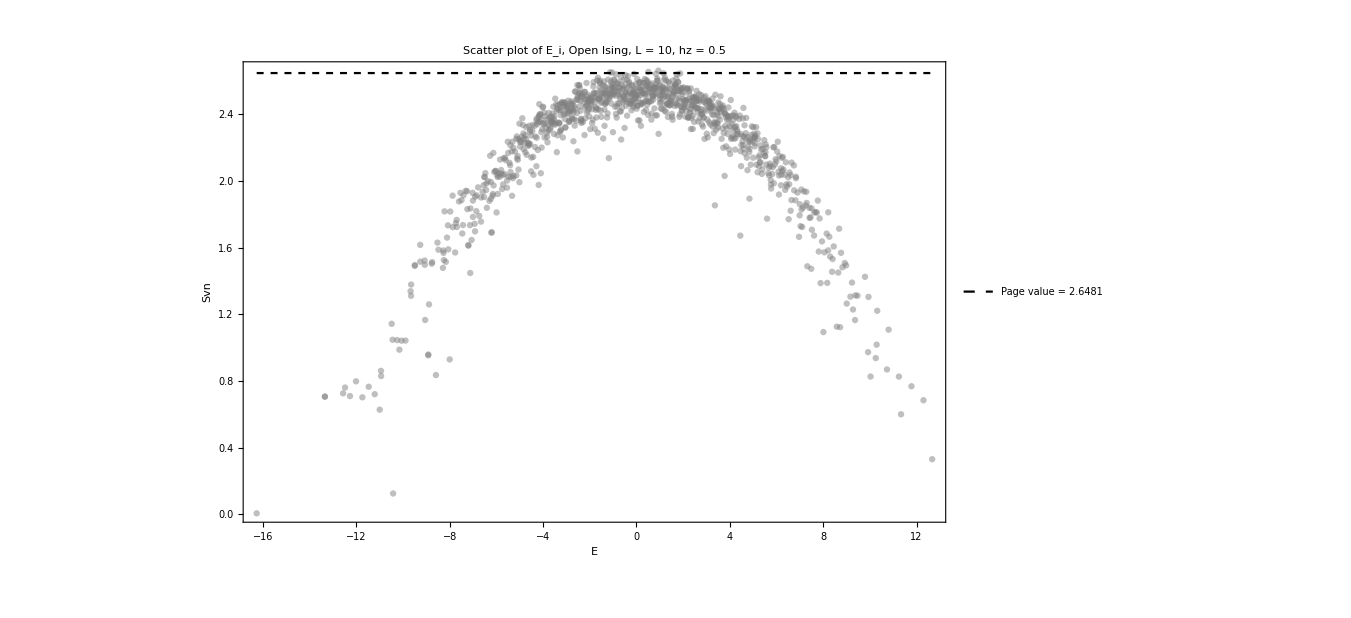

```mathematica
Show[{ListPlot[Transpose[{eigenval,sdiageigenvec}],PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of E_i, Open Ising, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",35,Black],PlotStyle->{Directive[Gray,Opacity[0.5]]},PlotRange->All,ImageSize->1000,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],Style["Svn"]}],Plot[pageEntropy[La,Lb],{x,Min[eigenval],Max[eigenval]},PlotStyle->{Directive[Black,Dashed]},PlotLegends->{Style["Page value = "<>ToString[N[pageEntropy[La,Lb]]],20,Black]}]},PlotRange->All]
```

# Ising scatter plots

```mathematica
L=5;
hx=1;
J=1;
hz=0.5;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
La=1;
Lb=L-La;
sdiageigenvec=ParallelTable[sdiag[L,La,Lb,i],{i,eigenvec},DistributedContexts->Full];
```

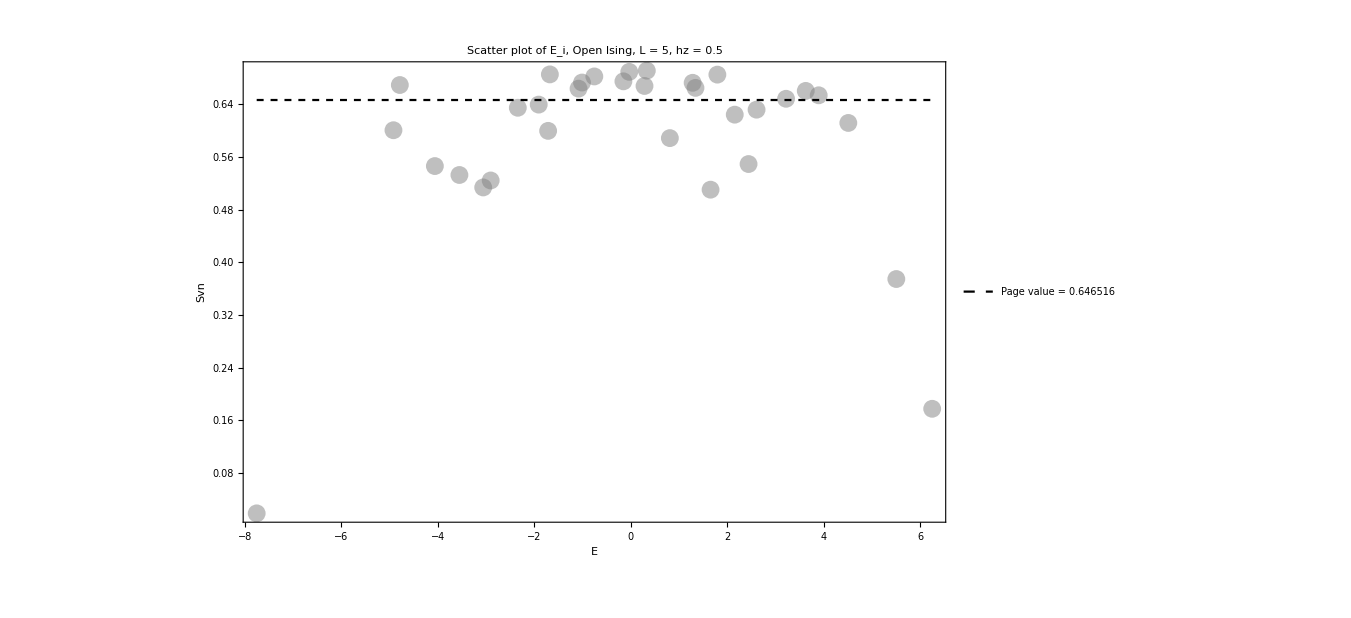

```mathematica
Show[{ListPlot[Transpose[{eigenval,sdiageigenvec}],PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of E_i, Open Ising, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",35,Black],PlotStyle->{Directive[Gray,Opacity[0.5]]},PlotRange->All,ImageSize->1000,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],Style["Svn"]}],Plot[pageEntropy[La,Lb],{x,Min[eigenval],Max[eigenval]},PlotStyle->{Directive[Black,Dashed]},PlotLegends->{Style["Page value = "<>ToString[N[pageEntropy[La,Lb]]],20,Black]}]},PlotRange->All]
```

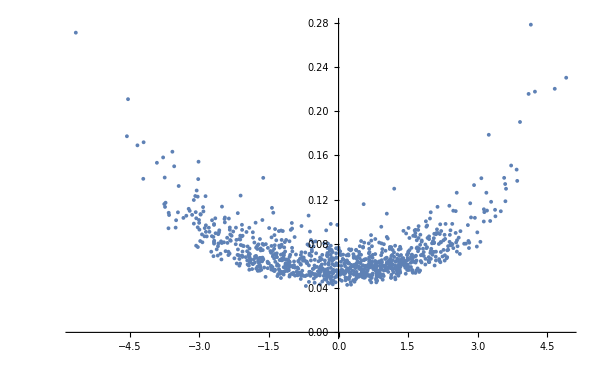

```mathematica
productstate2=Table[RandomChainProductState[L],1000];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[eigenvec].i]^4]],{i,productstate2},DistributedContexts->Full];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstate2},DistributedContexts->Full];
ListPlot[Transpose[{energies,iprs}],PlotRange->All,ImageSize->600]
```

```mathematica
data=SortBy[Transpose[{iprs,energies,productstate2}],First];
productstate=data[[1;;-1;;200]][[All,3]];
tlist=Table[10^i,{i,-2,12,0.01}];
tlist//Length
```

1401

```mathematica
neweigenval=RandomReal[{-1,1},2^L];
```

```mathematica
fakesvn=Table[ParallelTable[{t,svn[L,La,Lb,i,eigenval,eigenvec,t]},{t,tlist},DistributedContexts->Full],{i,productstate}];
```

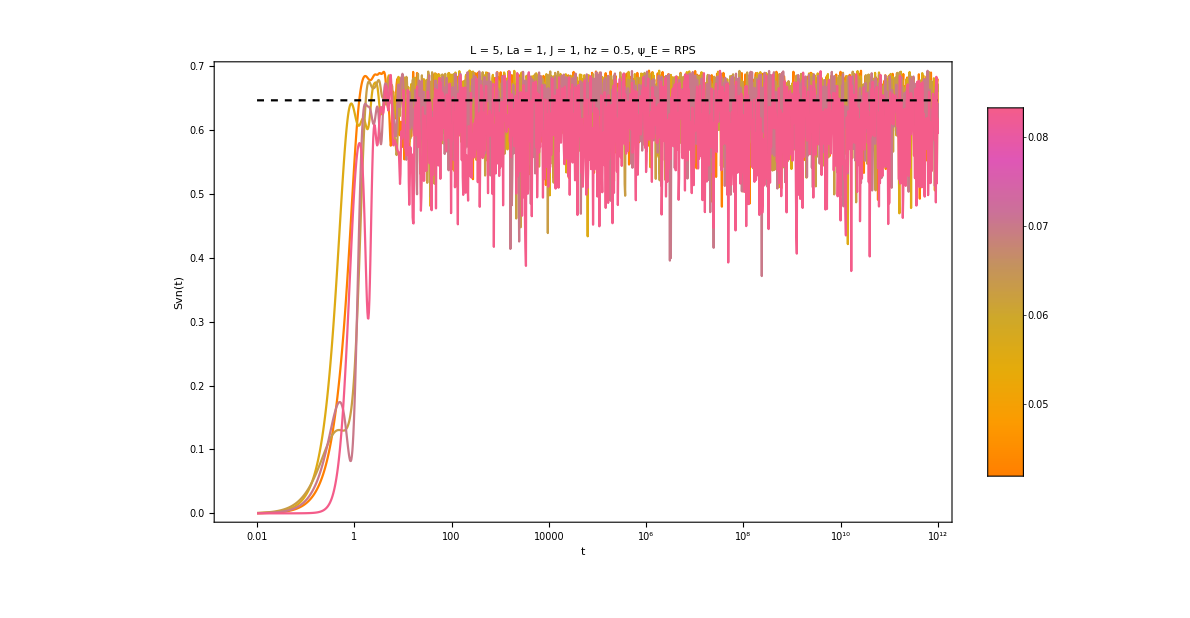

```mathematica
(*Step 1:Determine the overall energy range*)
sorted=data[[1;;-1;;200]][[All,1]];
{Emin,Emax}={Min[sorted],Max[sorted]};
(*Step 2:Define a function to map an energy value to a temperature-like color*)
colorMapping[e_]:=ColorData["FruitPunchColors"][Rescale[e,{Emin,Emax}]];
(*plot*)
plots=Table[ListLogLinearPlot[fakesvn[[i]],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[hz]<>", ψ_E = RPS",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotStyle->Directive[colorMapping[sorted[[i]]]]],{i,Length[productstate]}];
Legended[Show[{plots,LogLinearPlot[pageEntropy[La,Lb],{x,Min[tlist],Max[tlist]},PlotStyle->{Directive[Black,Dashed]}]}],BarLegend[{"FruitPunchColors",{Emin,Emax}},LabelStyle->{FontSize->12}]]
```

# Ising symmetric states

```mathematica
Clear[svnb];
svnb[L_,La_,Lb_,ini_,site_,eigenval_,eigenvec_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=Chop[MatrixPartialTrace[Dyad[state],{1,2,3,4},2]];
Chop[Total[Map[VNentropy,Chop[Eigenvalues[rho]]]]]
];
```

```mathematica
L=5;
hx=1;
J=1;
hz=0.5;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
La=1;
Lb=L-La;
sdiageigenvec=ParallelTable[sdiag[L,La,Lb,i],{i,eigenvec},DistributedContexts->Full];
```

```mathematica
Show[{ListPlot[Transpose[{eigenval,sdiageigenvec}],PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of E_i, Open Ising, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",35,Black],PlotStyle->{Directive[Gray,Opacity[0.5]]},PlotRange->All,ImageSize->1000,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],Style["Svn"]}],Plot[pageEntropy[La,Lb],{x,Min[eigenval],Max[eigenval]},PlotStyle->{Directive[Black,Dashed]},PlotLegends->{Style["Page value = "<>ToString[N[pageEntropy[La,Lb]]],20,Black]}]},PlotRange->All]
```

-Graphics-

```mathematica
uno=RandomChainProductState[1];
dos=RandomChainProductState[1];
tres=RandomChainProductState[1];
```

```mathematica
productstate=Flatten[KroneckerProduct[uno,dos,tres,dos,uno],1];
```

```mathematica
Dyad[uno]//MatrixForm
```

(0.0825585 | 0.120537-0.247413 ⅈ
0.120537+0.247413 ⅈ | 0.917441+0. ⅈ)

```mathematica
Chop[MatrixPartialTrace[Dyad[productstate],{1,2,3,4},2]]//MatrixForm
Chop[MatrixPartialTrace[Dyad[productstate],{2,3,4,5},2]]//MatrixForm
```

(0.0825585 | 0.120537-0.247413 ⅈ
0.120537+0.247413 ⅈ | 0.917441)

(0.0825585 | 0.120537-0.247413 ⅈ
0.120537+0.247413 ⅈ | 0.917441)

```mathematica
tlist=Table[10^i,{i,-2,12,0.01}];
tlist//Length
```

1401

```mathematica
svn=ParallelTable[{t,svn[L,La,Lb,productstate,eigenval,eigenvec,t]},{t,tlist},DistributedContexts->Full];
```

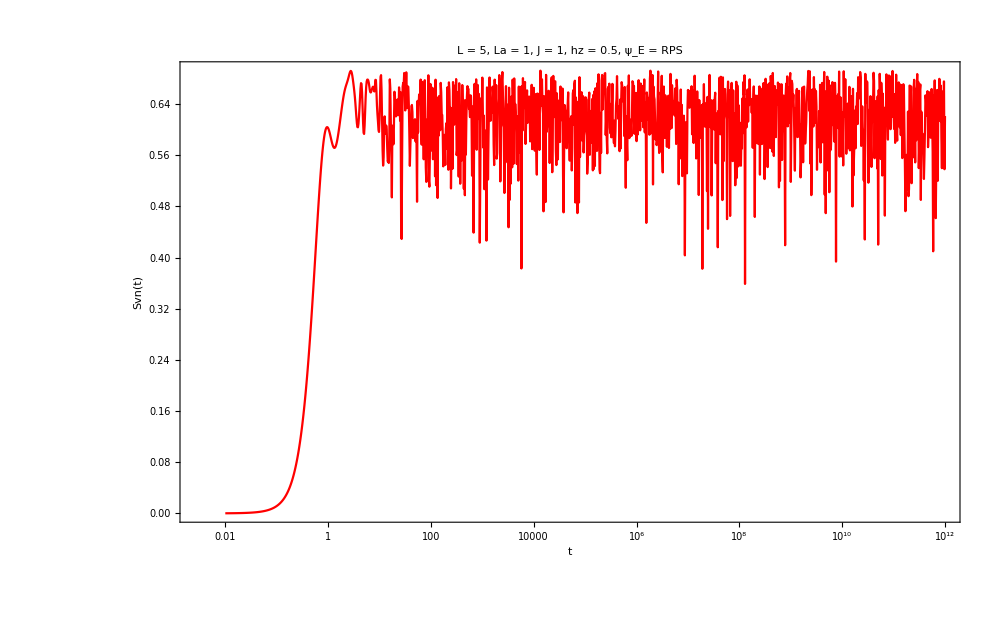

```mathematica
plot1=ListLogLinearPlot[svn,PlotStyle->Red,PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[hz]<>", ψ_E = RPS",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000]
```

```mathematica
fakesvnb=ParallelTable[{t,svnb[L,La,Lb,productstate,1,eigenval,eigenvec,t]},{t,tlist},DistributedContexts->Full];
```

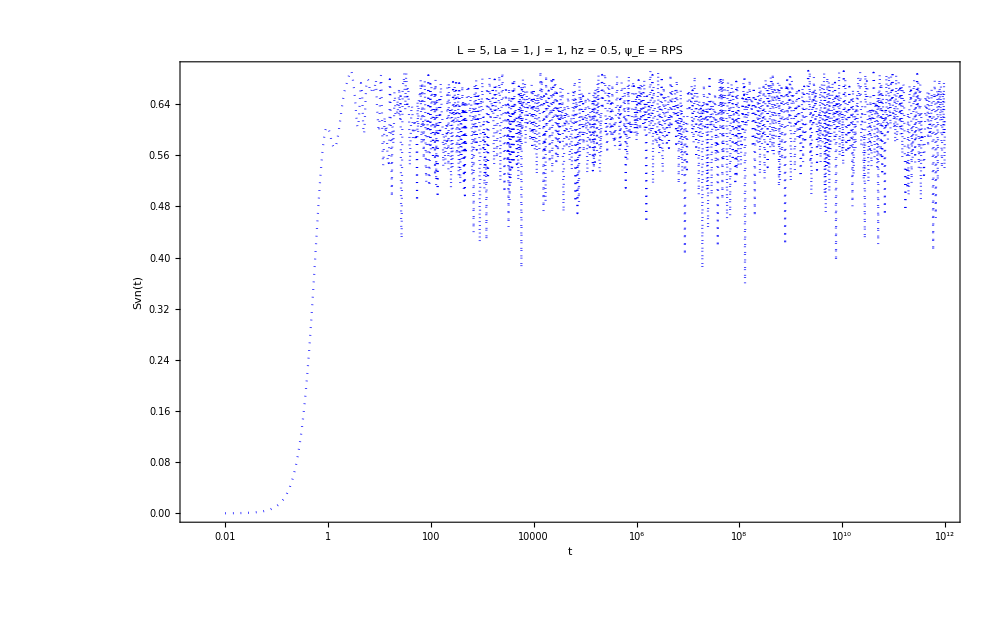

```mathematica
plot2=ListLogLinearPlot[fakesvnb,PlotStyle->Directive[Blue,Dotted],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[hz]<>", ψ_E = RPS",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000]
```

```mathematica
fakesvnc=ParallelTable[{t,svnb[L,La,Lb,productstate,1,eigenval,eigenvec,t]},{t,tlist},DistributedContexts->Full];
```

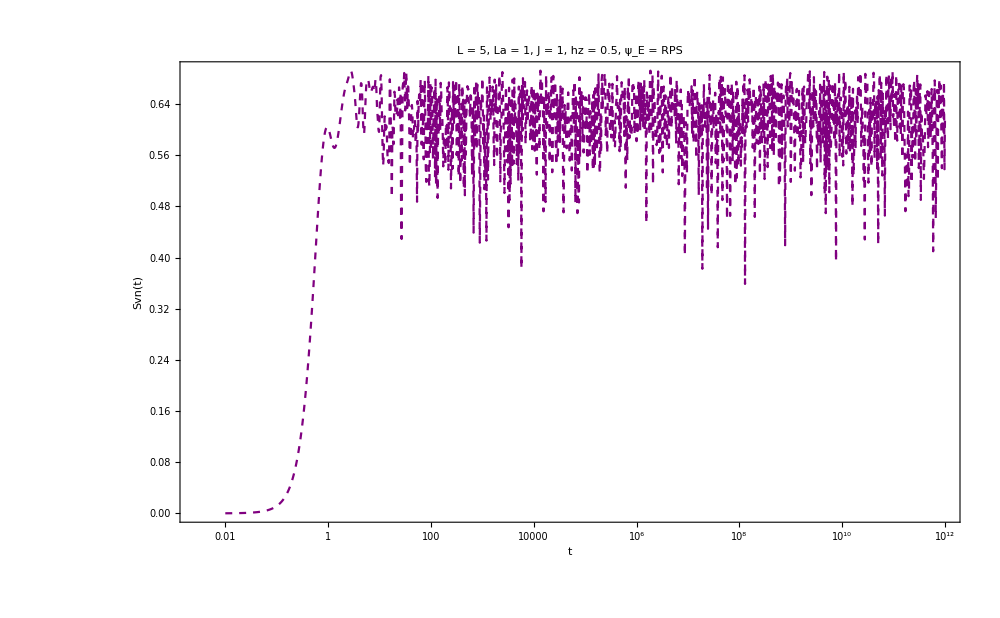

```mathematica
plot3=ListLogLinearPlot[fakesvnc,PlotStyle->Directive[Purple,Dashed],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[hz]<>", ψ_E = RPS",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000]
```

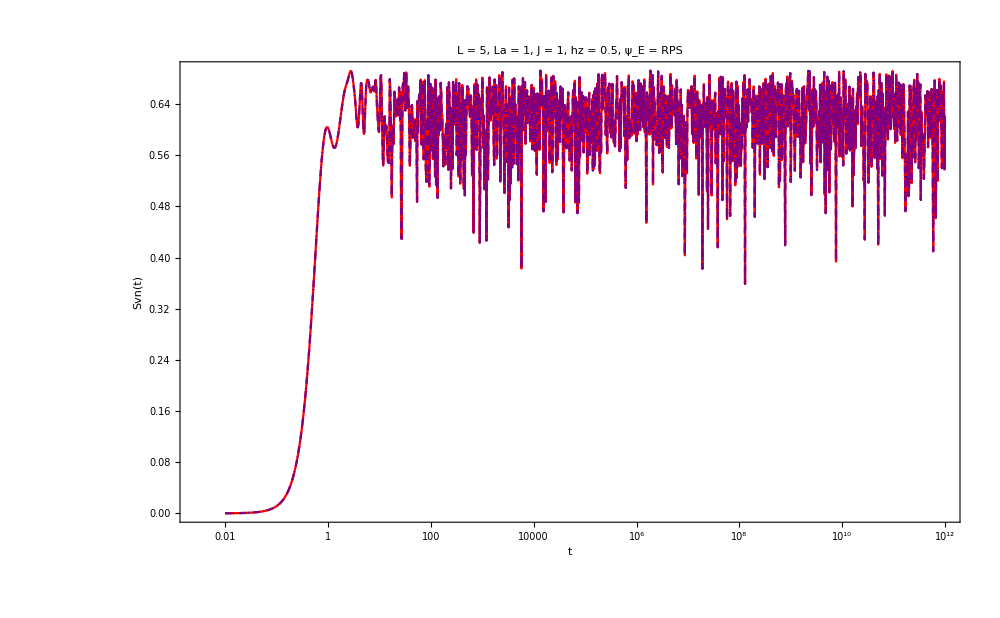

```mathematica
Show[{plot1,plot2,plot3}]
```

```mathematica
fakesvn=ParallelTable[{t,svnb[L,La,Lb,productstate,1,eigenval,eigenvec,t]},{t,tlist},DistributedContexts->Full];
```

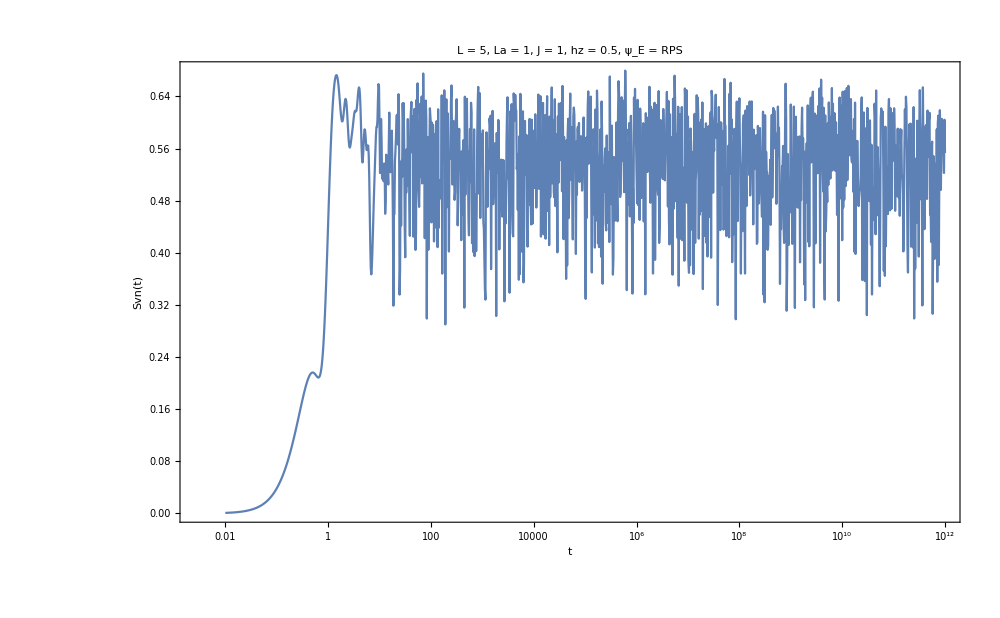

```mathematica
plot4=ListLogLinearPlot[fakesvn,PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[hz]<>", ψ_E = RPS",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000]
```

# Choi matrix ising

## RPS ψ_E

```mathematica
Lb=L-La;
ψ=productstate[[i]];
rho=MatrixPartialTrace[Dyad[ψ],1,{2^La,2^Lb}];
A=KroneckerProduct[IdentityMatrix[2^(Lb),SparseArray]/2^(La),rho];
```

```mathematica
allplots={};
```

```mathematica
Do[

Lb=L-La;
ψ=productstate[[i]];
rho=MatrixPartialTrace[Dyad[ψ],1,{2^La,2^Lb}];
A=KroneckerProduct[IdentityMatrix[2^(Lb),SparseArray]/2^(La),rho];
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvals,eigenvecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
P=Transpose[eigenvecs];
Pinv=Conjugate[eigenvecs];
ClearAll[U];
U[t_]:=P.DiagonalMatrix[Exp[-I*eigenvals*t]].Pinv;
chois=ParallelTable[ChoiMatrix[U[t],A,La,Lb],{t,tlist},DistributedContexts->Full];
purity=ParallelTable[Chop[Tr[i.i]],{i,Chop[chois]},DistributedContexts->Full];
plot=ListLogLinearPlot[Transpose[{tlist,purity}],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[hz]<>",RPS ψ_E",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Choi's Purity"]},PlotRange->All,ImageSize->1000,PlotStyle->Directive[colorMapping[sorted[[i]]]],PlotLegends->{Style["RPS ψ_E, IPR = "<>ToString[sorted[[i]]],Opacity[1.0]]}];
final=Show[{plot,LogLinearPlot[(1/2^La)^2,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]],LogLinearPlot[0.5,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Purple,Dashed]]}];
Export["choi_RPS_"<>ToString[i]<>"_loglinear_purity_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_J_"<>ToString[J]<>"_hz_"<>ToString[hz]<>"_.png",final,ImageResolution->300];
AppendTo[allplots,final];
,{i,Length[productstate]}];
Export["choi_RPS_ALL_loglinear_purity_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_J_"<>ToString[J]<>"_hz_"<>ToString[hz]<>"_.gif",allplots,"DisplayDurations"->1.0,"AnimationRepetitions"->Infinity]
```

choi_RPS_ALL_loglinear_purity_L_10_La_1_J_1_hz_3._.gif